```mathematica
rnew[x_,y_]= Sqrt[x^2+y^2];
```

```mathematica
λ = 0.800; (*microns*)
γ = π*1.0/180; (*rad*)
γ05 = π*0.5/180; (*rad*)
γ10 = π*1.0/180; (*rad*)
m = 5; (*bessel order*)
k = 2*π/λ; (*microns^-1*)
rp[x_] = k*Sin[x]; (*microns^-1*)
ein = 250*10^-3; (*J*)
tin = 50*10^-15; (*s*)
din = 4.0; (*cm*)
ain =π*(din/2)^2; (*cm^2*)
Pin = ein/(tin*ain); (*W/cm^2*)
zmax[x_] = din/(2*Tan[x]); (*cm*)
r2[x_] = 3.0542/rp[x] ;(*microns*)
r3[x_] = 4.2012/rp[x];(*microns*)
r4[x_] = 5.3175/rp[x]; (*microns*)
r5[x_] = 6.4156/rp[x];
r6[x_] = 7.5013/rp[x];
r7[x_] = 8.5778/rp[x];
r8[x_] = 9.6474/rp[x];
rp[γ]
```

0.137071

```mathematica
Needs["PlotLegends`"];Plot[{r2[π*x/180],r3[π*x/180],r4[π*x/180],r5[π*x/180],r6[π*x/180],r7[π*x/180],r8[π*x/180]},{x,0.1,3},AxesLabel->{"γ (deg)","r (μm)"},AxesOrigin->{0,0},PlotLegend->{"J_2","J_3","J_4","J_5","J_6","J_7","J_8"},PlotLabel->"Channel Radii vs. Convergence Angle"]
```

PlotLegend::shdw: Symbol "PlotLegend" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

Plot::optx: Unknown option Global`PlotLegend in {r2[π x/180], r3[π x/180], r4[π x/180], r5[π x/180], r6[π x/180], r7[π x/180], r8[π x/180]}, {x, 0.1`, 3}, AxesLabel → {.

Plot[{r2[(π x)/180],r3[(π x)/180],r4[(π x)/180],r5[(π x)/180],r6[(π x)/180],r7[(π x)/180],r8[(π x)/180]},{x,0.1,3},AxesLabel→{γ (deg),r (μm)},AxesOrigin→{0,0},Global`PlotLegend→{J_2,J_3,J_4,J_5,J_6,J_7,J_8},PlotLabel→Channel Radii vs. Convergence Angle]

```mathematica
r5[γ]
```

46.805

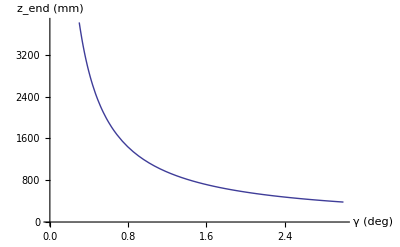

```mathematica
Plot[10*zmax[π*x/180],{x,0.3,3},AxesOrigin->{0,0},PlotRange->Full,AxesLabel->{"γ (deg)","z_end (mm)"}]
```

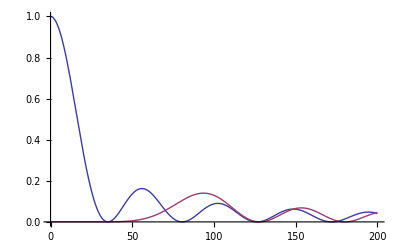

```mathematica
Plot[{BesselJ[0,k*Sin[γ05]*r]^2,BesselJ[5,k*Sin[γ05]*r]^2},{r,0,200},PlotRange->{0,1}]
```

```mathematica
Subscript[c, α][x_] = π*Sin[x]^2 * (1+Cos[x])^2/(2*Cos[x]);
P5[r_,z_] = Pin*Subscript[c, α][γ05]*k*1000*z*BesselJ[5,k*Sin[γ05]*r]^2;
P4[r_,z_] = Pin*Subscript[c, α][γ05]*k*1000*z*BesselJ[4,k*Sin[γ05]*r]^2;
P3[r_,z_] = Pin*Subscript[c, α][γ05]*k*1000*z*BesselJ[3,k*Sin[γ05]*r]^2;
P2[r_,z_] = Pin*Subscript[c, α][γ05]*k*1000*z*BesselJ[2,k*Sin[γ05]*r]^2;
P0[r_,z_] = Pin*Subscript[c, α][γ05]*k*1000*z*BesselJ[0,k*Sin[γ05]*r]^2;
P52[r_,z_] = Pin*Subscript[c, α][γ10]*k*1000*z*BesselJ[5,k*Sin[γ10]*r]^2;
P42[r_,z_] = Pin*Subscript[c, α][γ10]*k*1000*z*BesselJ[4,k*Sin[γ10]*r]^2;
P32[r_,z_] = Pin*Subscript[c, α][γ10]*k*1000*z*BesselJ[3,k*Sin[γ10]*r]^2;
P22[r_,z_] = Pin*Subscript[c, α][γ10]*k*1000*z*BesselJ[2,k*Sin[γ10]*r]^2;
P02[r_,z_] = Pin*Subscript[c, α][γ10]*k*1000*z*BesselJ[0,k*Sin[γ10]*r]^2;
```

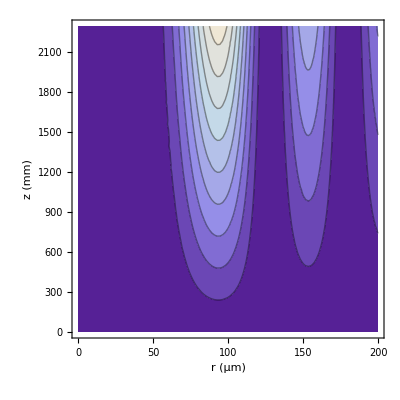

```mathematica
ContourPlot[P5[r,z],{r,0,200},{z,0,zmax[γ]*10},AxesLabel->{"r (μm)","z (mm)"},PlotRange->{0,5*10^14}]
```

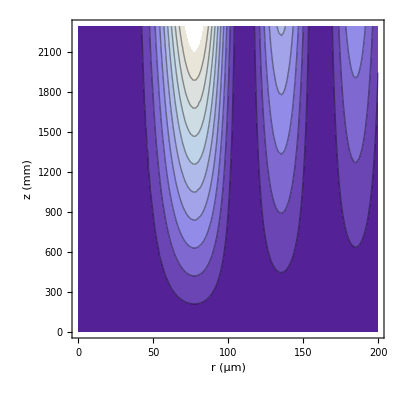

```mathematica
ContourPlot[P4[r,z],{r,0,200},{z,0,zmax[γ]*10},AxesLabel->{"r (μm)","z (mm)"},PlotRange->{0,5*10^14}]
```

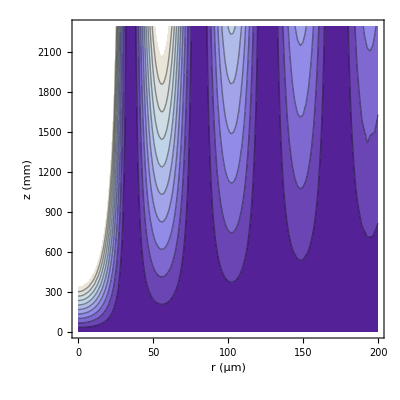

```mathematica
ContourPlot[P0[r,z],{r,0,200},{z,0,zmax[γ]*10},AxesLabel->{"r (μm)","z (mm)"},PlotRange->{0,5*10^14}]
```

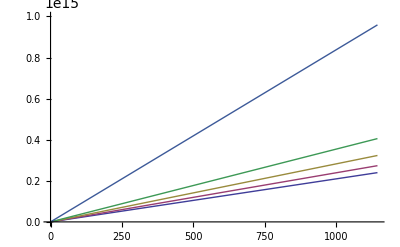

```mathematica
Plot[{P5[r5[γ05],z],P4[r4[γ05],z],P3[r3[γ05],z],P2[r2[γ05],z],P52[r5[γ10],z],P42[r4[γ10],z],P32[r3[γ10],z],P22[r2[γ10],z]},{z,0,zmax[γ]*10}]
```

```mathematica
P42[r4[γ10],900]
```

8.597×10^14

```mathematica
NSolve[P[r5[γ],z]==1.5*10^14,z]
zmax[γ]*10
```

{{z→2439.88}}

2291.77

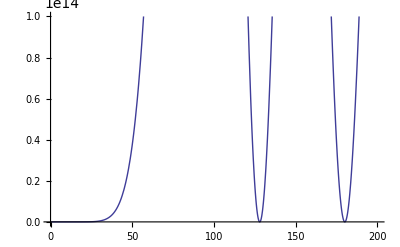

```mathematica
Plot[P[r,zmax[γ]*10],{r,0,200},PlotRange->{0,1*10^14}]
```

```mathematica
ContourPlot[Pin*Subscript[c, α][γ]*k*1000*500*BesselJ[5,rnew[k*Sin[γ]*x,k*Sin[γ]*y]]^2,{x,-200,200},{y,-200,200},PlotRange->{0,1*10^14},PlotPoints->50,ColorFunction->"BlueGreenYellow",AxesLabel->{"x (μm)","y (μm)"}]
```

```mathematica
ContourPlot[Pin*Subscript[c, α][γ]*k*1000*500*BesselJ[0,rnew[k*Sin[γ]*x,k*Sin[γ]*y]]^2,{x,-200,200},{y,-200,200},PlotRange->{0,1*10^14},PlotPoints->50,ColorFunction->"BlueGreenYellow",AxesLabel->{"x (μm)","y (μm)"}]
```

-Graphics-